```mathematica
(* The Base directory when working on the lab computer *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research"}];
labComp=FileNameJoin[{"C:","Users","karl",dropBoxOn}];
homeComp=FileNameJoin[{"/","home","karl",dropBoxOn}];
(* Good graphing setup *)
labelSize=18;
(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{homeComp}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=1,i<=Length[directories],i++,
Print[i -> directories[[i]]];]
```

/home/karl/Dropbox/00School/research

1→3_15_17_AimingFor5e12

2→4-18-17

3→4-22-17

4→data

5→Data Before 4-1-17

6→firstRun2017

7→labBook

8→legacy

9→machineShopOrders

10→mathematicaCode

11→mathematicaRb

12→operationManuals

13→papers

14→polarization_4-18-17

15→polarization_4-4-17

16→polarization_4-6-17

17→probeLaserPower

18→pumpLaserFindingCircular_3-29_17

19→RbControlPiPrograms

20→rbsim

21→requisitions

22→wavemeterNoRb

23→wavemeterReliability_3-30-17

24→wmReliability_4-7-17

17→RbControlPiPrograms

18→rbsim

19→requisitions

20→wavemeterNoRb

21→wavemeterReliability_3-30-17

22→wmReliability_4-7-17

```mathematica
(* set rootFolder to the folder name containing the RbPolarization Files *)
rootFolder=FileNameJoin[{dataFolder,directories[[3]],"lowDensityRun"}];
SetDirectory[rootFolder];
(* Obtain the filename of the absorption data *)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
For[i=1,i<=Length[scanFiles],i++,
Print[i -> scanFiles[[i]]];]
```

1→FDayScan2017-04-23_030729RotationAnalysis.dat

2→FDayScan2017-04-23_031534RotationAnalysis.dat

3→FDayScan2017-04-23_032338RotationAnalysis.dat

4→FDayScan2017-04-23_033307RotationAnalysis.dat

5→FDayScan2017-04-23_034110RotationAnalysis.dat

6→FDayScan2017-04-23_034914RotationAnalysis.dat

7→FDayScan2017-04-23_035826RotationAnalysis.dat

8→FDayScan2017-04-23_040145RotationAnalysis.dat

9→FDayScan2017-04-23_040500RotationAnalysis.dat

10→FDayScan2017-04-23_040922RotationAnalysis.dat

11→FDayScan2017-04-23_041243RotationAnalysis.dat

12→FDayScan2017-04-23_041605RotationAnalysis.dat

13→FDayScan2017-04-23_042059RotationAnalysis.dat

14→FDayScan2017-04-23_042416RotationAnalysis.dat

15→FDayScan2017-04-23_042735RotationAnalysis.dat

16→FDayScan2017-04-23_043117RotationAnalysis.dat

17→FDayScan2017-04-23_043745RotationAnalysis.dat

18→FDayScan2017-04-23_044417RotationAnalysis.dat

```mathematica
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelA2=a1/(δ)^2+θ0;
modelB4=a1/(δ-b)^2+a2/(δ-b)^4+θ0;
modelB2=a1/(δ-b)^2+θ0;
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit},
validEntries=data[Select[#[[columnMissing]]>7000000&]];
referenceSpacing=data[[2]][[columnReference]]-data[[1]][[columnReference]];
j=1;
While[And[Length[adjacentSpots]<3,j*referenceSpacing<1024],
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]<=referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
fit[missingEntry]
];

FillInMissedFrequencies[data_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,position,approxValue,data2,k},
data2=data;
dataCopy=Dataset[Take[data,{1,-1},{1,2}]];
missingEntries=dataCopy[Select[#[[columnMissing]]<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
data2[[position,columnMissing]]=approxValue;
];
data2
];

StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

SetAsymptoteToZero[data_,nearResCutoff_,farResCutoff_]:=Module[{model,dataCopy,nlmFit,replacements},
dataCopy=Dataset[data];
dataCopy=dataCopy[Select[Abs[#[[1]]]>nearResCutoff&]];
dataCopy=dataCopy[Select[Abs[#[[1]]]<farResCutoff&]];
Print[dataCopy];
model=a1/(δ)^2+a2/(δ)^4+θ0;
nlmFit =NonlinearModelFit[Normal[dataCopy],model,{{a1,1},{a2,1},{θ0,33}},δ];
replacements=nlmFit["BestFitParameters"];

dataCopy=Transpose[Normal[dataCopy]];
dataCopy[[2]]=dataCopy[[2]]-θ0/.replacements;
Transpose[{dataCopy[[1]]-detuningOffset,dataCopy[[2]]}]
]
```

65.3

64.5

105.52-0.394071 x+0.759312 x^2

{{-4.95609,26.0316},{-6.25264,25.8185},{-7.54918,25.7833},{-8.84571,25.7517},{-10.1422,25.781},{-11.4387,25.7621},{-12.7353,25.8369},{-14.0317,25.9916},{-15.3282,26.0196},{-16.6247,26.0344},{-17.9212,26.2491},{-19.2176,26.212},{-20.5141,26.4507},{-21.8105,26.5681},{-23.107,26.6965},{-24.4034,26.8995},{-25.6998,27.078},{-26.9962,27.2145},{-28.2926,27.3791},{-29.589,27.4465}}

First::nofirst: {} has zero length and no first element.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::dotsh: Tensors {} and {{0,1},{0,0}} have incompatible shapes.

Set::partw: Part 1 of {} does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

First::nofirst: {} has zero length and no first element.

Dot::dotsh: Tensors {} and {{0,1},{0,0}} have incompatible shapes.

Set::partw: Part 1 of {} does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Dot::dotsh: Tensors {} and {{0,1},{0,0}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Set::partw: Part 1 of {} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

{{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][0]),29.0924},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][50]),28.3817},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][100]),29.319},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][150]),28.7713},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][200]),29.44},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][250]),28.1821},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][300]),28.4922},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][350]),28.8164},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][400]),29.2471},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][450]),29.0698},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][500]),29.1242},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][550]),29.2001},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][600]),29.0476},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][650]),28.9849},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][700]),29.4479},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][750]),28.7619},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][800]),28.4955},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][850]),28.8235},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][900]),28.6286},{-377107.+(2.99792×10^12)/(LinearModelFit[{},x,x][950]),29.042}}

{{#File:,/home/pi/RbData/2017-04-23/FDayScan2017-04-23_032338.dat},{#Comments:,Polarization, high magnets, full pump side flourescence, s- pump},{#IonGauge(Torr):,0.000152},{#CVGauge(N2)(Torr):,0.0986},{#CVGauge(He)(Torr):,0.000115},{#CurrTemp(Res):,111.9},{#SetTemp(Res):,112.},{#CurrTemp(Targ):,139.9},{#SetTemp(Targ):,140.},{#ProbeOffset:,25.},{#Mag1Voltage:,65.3},{#Mag2Voltage:,64.5},{#Revolutions:,1},{#DataPointsPerRev:,50},{Aout,Wavelength,c0,s2,s2Err+,s2Err-,c2,c2Err+,c2Err-,angle,angleErr+,angleErr-,homeFlag},{0,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{50,-8.,-2.4981,0.003633,0.000378,0.000378,0.00502,0.000393,0.000393,27.0547,1.70094,1.84778,0},{100,-8.,-2.49628,0.006292,0.000376,0.000376,0.007418,0.000384,0.000384,24.8483,1.08725,1.14798,0},{150,-8.,-2.50099,0.000222,0.000361,0.000361,0.000403,0.000367,0.000367,30.5715,14.7103,35.2954,0},{200,-8.,-2.50117,0.000064,0.00036,0.00036,0.000068,0.00036,0.00036,23.3672,25.6298,86.5632,0},{250,-8.,-2.50106,0.000227,0.000362,0.000362,0.000241,0.000362,0.000362,23.3926,16.6651,52.0539,0},{300,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{350,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{400,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{450,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{500,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{550,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{600,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{650,7.95029×10^6,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{700,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{750,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{800,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{850,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{900,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0},{950,-8.,-2.50122,0.,0.000359,0.000359,0.,0.000359,0.000359,-40.7346,94.9146,49.4407,0}}

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

General::stop: Further output of LinearModelFit::rank will be suppressed during this calculation.

{{377060.,-40.7346},{323191.,27.0547},{276504.,24.8483},{235654.,30.5715},{199609.,23.3672},{167569.,23.3926},{138902.,-40.7346},{113101.,-40.7346},{89758.2,-40.7346},{68537.,-40.7346},{49161.1,-40.7346},{31400.,-40.7346},{15059.7,-40.7346},{-23.6919,-40.7346},{-13989.8,-40.7346},{-26958.2,-40.7346},{-39032.4,-40.7346},{-50301.5,-40.7346},{-60843.7,-40.7346},{-70726.9,-40.7346}}

First::nofirst: {} has zero length and no first element.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::dotsh: Tensors {} and {{0,1},{0,0}} have incompatible shapes.

Set::partw: Part 1 of {} does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

First::nofirst: {} has zero length and no first element.

Dot::dotsh: Tensors {} and {{0,1},{0,0}} have incompatible shapes.

Set::partw: Part 1 of {} does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Dot::dotsh: Tensors {} and {{0,1},{0,0}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Set::partw: Part 1 of {} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

-Graphics-

-Graphics-

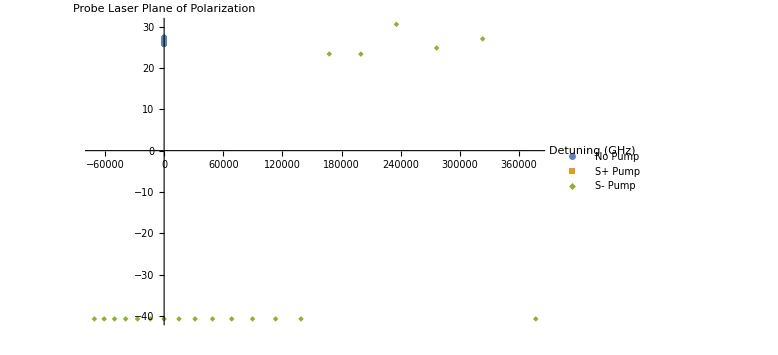

-Graphics-

```mathematica
(* Define important constants of data processing *)
firstFaradayFileNumber=1;
detuningOffset=1.144;
rotAnalDataStartRow=16;
wavelengthColumn=2;
angleColumn=10;

(* Define important physical constants*)
c=2.99792458*^8;
ν0=377107.463;
(* Retrieves the recorded voltages of the magnets *)
rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber]]}],"tsv"];
v1=rotationAnalysisData[[11]][[2]]
v2=rotationAnalysisData[[12]][[2]]
(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1=v1*c1v2iSlope+c1v2iInt;
i2=v2*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2)  ;
getBEq[i1,i2]
BdotL=Integrate[getBEq[i1,i2],{x,0,2.794}] /100/10000;(* Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)



rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
noPump=ConvertFDayWavelengthToDetune[rotationAnalysisData]


rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber+1]]}],"tsv"];
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
sPlusPump=ConvertFDayWavelengthToDetune[rotationAnalysisData]


rotationAnalysisData=Import[FileNameJoin[{rootFolder,scanFiles[[firstFaradayFileNumber+2]]}],"tsv"]
rotationAnalysisData=StripFaradayData[rotationAnalysisData];
rotationAnalysisData=FillInMissedFrequencies[rotationAnalysisData,2,1];
rotationAnalysisData=Take[rotationAnalysisData,All,{2,-1}];
sMinusPump=ConvertFDayWavelengthToDetune[rotationAnalysisData]


{detune,θm}=Transpose[sMinusPump];
{detune,θm}={detune,θm};
sMinusPump=Transpose[{detune,θm}];
{detune,θp}=Transpose[sPlusPump];
pumpDifference=Transpose[{detune-detuningOffset,θp-θm}];
differencePlot=ListPlot[Legended[pumpDifference,"(S+) - (S-)"],AxesLabel->{"Detuning (GHz)","Linear Pol. Angle"},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},ImageSize->Large]
Rasterize[differencePlot]
allPlot=ListPlot[{Legended[noPump,"No Pump"],Legended[sPlusPump,"S+ Pump"],Legended[sMinusPump,"S- Pump"]},PlotRange->All,LabelStyle->18,PlotMarkers->{Automatic,Large},ImageSize->Large,AxesLabel->{"Detuning (GHz)","Probe Laser\nPlane of Polarization"}]
Rasterize[allPlot]
```

FittedModel[-0.417695-71.8261 x]

Integrated Magnetic Field (T*m):

0.000298806

Number Density (cm^-3):

Slope:

-71.8261

Polarization:

-0.282958

Polarization Uncertainty:

0.142066

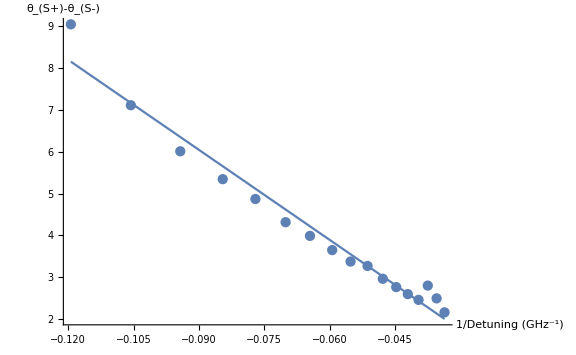

```mathematica
(* Calculates fit for data *)
(* Removes datapoints that wrapped in rotation *)
lowerBoundDetuning=8;
upperBoundDetuning=30;

pumpDiff=Dataset[pumpDifference];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]<upperBoundDetuning&]];
pumpDiff=pumpDiff[Select[Abs[#[[1]]]>lowerBoundDetuning&]];
pumpDiff=Normal[pumpDiff];
labelSize=18;

Clear[a,b,c,d,e]

(* Calculates fit for polarization *)
{detune,δθ}=Transpose[pumpDiff];
newThing=Transpose[{1/detune,δθ}];
lm=LinearModelFit[newThing,x,x]
polPlot=Plot[lm[x],{x,1/Min[detune],1/Max[detune]}];

slope=lm["BestFitParameters"][[2]];

Cpar=1.2692*^-11;
c=2.99792458*^8;
re=2.8179*^-15;
fge=0.34231;
k=4/3;
Print["Integrated Magnetic Field (T*m):"]
BdotL
μ=9.2740*^-24;
h=6.6261*^-34;
ν0=377107.463;
conversionFactor=h/(BdotL*c*re*fge*k*μ)*10^18*10^-6;(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

Print["Number Density (cm^-3):"]
n=1*^13;
Print["Slope:"];
Print[slope];
Print["Polarization:"]
pol=slope/(Cpar*n*2)
σSlope=lm["ParameterErrors"][[2]];
σDensity=5*^12;
Print["Polarization Uncertainty:"]
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)]
Show[{ListPlot[newThing],polPlot},PlotRange->All,AxesLabel->{"1/Detuning\n(GHz^-1)","θ_(S+)-θ_(S-)"},LabelStyle->labelSize,ImageSize->Large]
```